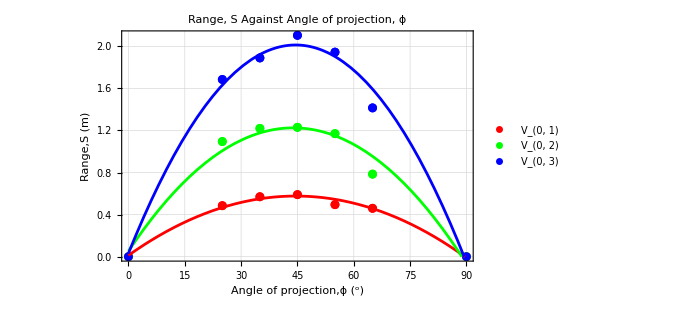

```mathematica
V1={{0,0},{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460},{90,0}};
V2={{0,0},{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785},{90,0}};
V3={{0,0},{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415},{90,0}};

V1error={
{Around[25,1],Around[0.485,0.01]},{Around[35,1],Around[0.570,0.01]},{Around[45,1],Around[0.590,0.01]},{Around[55,1],Around[0.495,0.01]},{Around[65,1],Around[0.460,0.01]}};
V2error={
{Around[25,1],Around[1.095,0.01]},{Around[35,1],Around[1.220,0.01]},{Around[45,1],Around[1.230,0.01]},{Around[55,1],Around[1.170,0.01]},{Around[65,1],Around[0.785,0.01]}};
V3error={
{Around[25,1],Around[1.685,0.01]},{Around[35,1],Around[1.890,0.01]},{Around[45,1],Around[2.105,0.01]},{Around[55,1],Around[1.945,0.01]},{Around[65,1],Around[1.415,0.01]}};

(*Extracting x and y values for each group*)
x1=V1[[All,1]];
y1=V1[[All,2]];
x2=V2[[All,1]];
y2=V2[[All,2]];
x3=V3[[All,1]];
y3=V3[[All,2]];

(*Fitting curves for each group*)
fit1=Fit[Transpose[{x1,y1}],{1,x,x^2},x];
fit2=Fit[Transpose[{x2,y2}],{1,x,x^2},x];
fit3=Fit[Transpose[{x3,y3}],{1,x,x^2},x];

(*Plotting the data points and best-fit curves with extended range*)
Show[
ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue}],
ListPlot[{V1error,V2error,V3error},PlotStyle->{Red,Green,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 2\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 3\)]\)"}],Plot[{fit1,fit2,fit3},{x,0,100},PlotStyle->{Red,Green,Blue},PlotRange->{{0,100},{0,Max[y3]}}],Frame->True,FrameLabel->{"Angle of projection,ϕ (^o)","Range,S (m)"},GridLines->Automatic,PlotLabel->"Range, S Against Angle of projection, ϕ",ImageSize->500]
```